```mathematica
Clear[blah]
Ne = 500;
 (* time in generations *)
(*tfin = 5000;*)
(*expcoeff=3;*)
(*n=18;*)
(* time in 2Neff generations *)
tfinC = 1;
x0 = 0.5;
ClearAll[delta];
delta[t_,eps_,dt_]:=1/dt*HeavisideTheta[t-eps]*HeavisideTheta[eps+dt-t]
(*selcoeff=4;*)
(*Clear[resultmat]*)
blah=NDSolve[{D[g[x,t],t] == -(2 Ne α Λ / W) Exp[2 Ne VG t / W]*x*(1-x)*D[g[x,t],x]+1/2*x*(1-x)*D[g[x,t],{x,2}],
g[x,0]==Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]x(1-x)],
g[0,t]==0,
g[1,t]==0}/.{α->.001,Λ->1,W->1, VG->0.0001111},
g,{x,0,1},{t,0.001,tfinC},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
blah
```

{{g→InterpolatingFunction[{{0., 1.}, {0.001, 1.}}, <>]}}

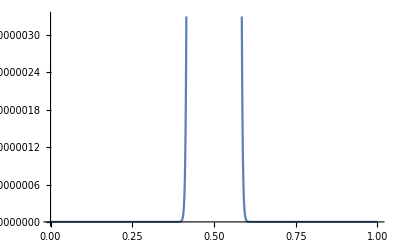

```mathematica
Plot[g[x,t]/(x(1-x))/. blah /. t->0.001, {x,0,1}]
```

```mathematica
Manipulate[Plot[g[x,t]/(x*(1-x)) /. blah, {x,0,1}], {t,0.001,1}]
```

ReplaceAll::reps: {blah} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
NIntegrate[Evaluate[g[x,0.25]/(x*(1-x)) /. blah],{x,0,1}]
```

{0.987312}

```mathematica
TriangularDistribution[{0.4999,0.5001},0.5]
```

TriangularDistribution[{0.4999,0.5001},0.5]

```mathematica
NIntegrate[Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]],{x,0,1}]
```

1.

```mathematica
NIntegrate[Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x] / (x(1-x))],{x,0,1}]
```

4.

```mathematica
Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]]
```

Piecewise[{{1.×10^8 (-0.4999+x), 0.4999≤x≤0.5}, {1.×10^8 (0.5001-x), 0.5<x≤0.5001}, {0, True}}]

```mathematica
Clear[blah]
Ne = 500;
 (* time in generations *)
(*tfin = 5000;*)
(*expcoeff=3;*)
(*n=18;*)
(* time in 2Neff generations *)
tfinC = 1;
x0 = 0.5;ClearAll[delta];
delta[t_,eps_,dt_]:=1/dt*HeavisideTheta[t-eps]*HeavisideTheta[eps+dt-t]
(*selcoeff=4;*)
(*Clear[resultmat]*)
blah=NDSolve[{D[g[x,t],t] == 1/2*x*(1-x)*D[g[x,t],{x,2}],
g[x,0]==0.25Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]],
g[0,t]==0,
g[1,t]==0},
g,{x,0,1},{t,0.001,tfinC},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
NIntegrate[Evaluate[g[x,0.25]/(x*(1-x)) /. blah],{x,0,1}]
```

{0.988603}

```mathematica
Manipulate[Plot[g[x,t]/(x*(1-x)) /. blah, {x,0,1},PlotRange->{{0,1},{-1,10}}], {t,0.001,1}]
```

```mathematica
Clear[blah]
Ne = 500;
 (* time in generations *)
(*tfin = 5000;*)
(*expcoeff=3;*)
(*n=18;*)
(* time in 2Neff generations *)
tfinC = 1;
x0 = 0.5;ClearAll[delta];
delta[t_,eps_,dt_]:=1/dt*HeavisideTheta[t-eps]*HeavisideTheta[eps+dt-t]
(*selcoeff=4;*)
(*Clear[resultmat]*)
blah=NDSolve[{D[f[x,t],t] == 1/2*D[f[x,t]*x*(1-x),{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]],
{D[f[x,t],x]/.{x->0}}==0,
{D[f[x,t],x]/.{x->1}}==0},
f,{x,0,1},{t,0.001,tfinC},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
NIntegrate[Evaluate[f[x,0.25]/. blah],{x,0,1}]
```

{0.988603}

```mathematica
NIntegrate[Evaluate[f[x,0.5]/. blah],{x,0,1}]
```

{0.866612}

```mathematica
Manipulate[Plot[f[x,t] /. blah, {x,0,1},PlotRange->{{0,1},{-1,10}}], {t,0.001,1}]
```

```mathematica
Clear[blah]
Ne = 500;
 (* time in generations *)
(*tfin = 5000;*)
(*expcoeff=3;*)
(*n=18;*)
(* time in 2Neff generations *)
tfinC = 1;
x0 = 0.5;ClearAll[delta];
delta[t_,eps_,dt_]:=1/dt*HeavisideTheta[t-eps]*HeavisideTheta[eps+dt-t]
(*selcoeff=4;*)
(*Clear[resultmat]*)
blah=NDSolve[{D[f[x,t],t] == 1/2*D[f[x,t]*x*(1-x),{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]]},
f,{x,0,1},{t,0.001,tfinC},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
NIntegrate[Evaluate[f[x,0.25]/. blah],{x,0,1}]
```

{0.988603}

```mathematica
NIntegrate[Evaluate[f[x,0.5]/. blah],{x,0,1}]
```

{0.866612}

```mathematica
Manipulate[Plot[f[x,t] /. blah, {x,0,1},PlotRange->{{0,1},{-1,10}}], {t,0.001,1}]
```

```mathematica
.001^2
.005^2
```

1.×10^-6

0.000025

```mathematica
Clear[blah];
Ne = 500;
 (* time in generations *)
(*tfin = 5000;*)
(*expcoeff=3;*)
(*n=18;*)
(* time in 2Neff generations *)
(*tfinC = 1;*)
(*x0 = 0.5;
ClearAll[delta];
delta[t_,eps_,dt_]:=1/dt*HeavisideTheta[t-eps]*HeavisideTheta[eps+dt-t]*)
(*selcoeff=4;*)
(*Clear[resultmat]*)
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{α->.005,Λ->1,W->1, θ ->.5},
g,{x,0,1},MaxStepSize->.000025];
blue=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{α->.005,Λ->1,W->1, θ ->1},
g,{x,0,1},MaxStepSize->.000025];
```

```mathematica
blah
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

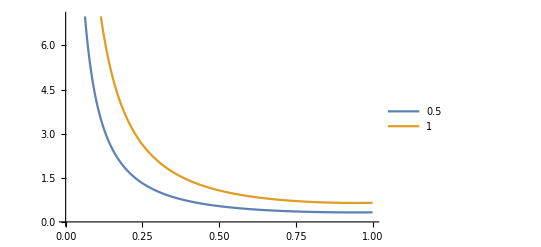

```mathematica
Plot[{g[x]/(x*(1-x)) /. blah,
g[x]/(x(1-x)) /. blue}, {x,0,1},PlotLegends->{.5,1}]
```

```mathematica
AUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.75022}

```mathematica
10 Ne
```

5000

```mathematica
1 - (1/5000)
```

4999/5000

```mathematica
N[4999/5000]
```

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(AUC 1-x) /. blah],{x,0.00001,.999999}]
```

{{0.0460453}}

```mathematica
2 500 .005
```

5.

```mathematica
2 500 .005^2
```

0.025